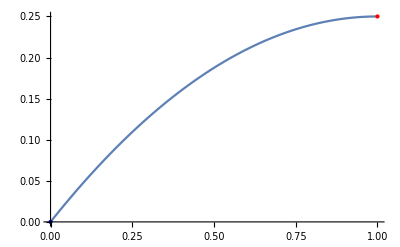
Funzione | Grafico | Massimo | Minimo
x/2-x^2/4 | -Graphics- | 1/4
x→1 | 0
x→0

```mathematica
Clear["Global`*"]
funzione=x/2-x^2/4;
incognita=x;
xmin=0;
xmax=1;

puntoMassimo={incognita/.Maximize[{funzione,xmin≤ incognita≤xmax},incognita][[2]],Maximize[{funzione,xmin≤ incognita≤xmax},incognita][[1]]};
puntoMinimo={incognita/.Minimize[{funzione,xmin≤ incognita≤xmax},incognita][[2]],Minimize[{funzione,xmin≤ incognita≤xmax},incognita][[1]]};
grafico=Plot[funzione,{x,xmin,xmax},Epilog->{{Blue,PointSize@Large,Point[puntoMinimo]},{Red,PointSize@Large,Point[puntoMassimo]}}];
allora=TableForm[{{"Funzione", "Grafico", "Massimo", "Minimo"}, {funzione, grafico, Maximize[{funzione,xmin≤ incognita≤xmax},incognita], Minimize[{funzione,xmin≤ incognita≤xmax},incognita]}}];
allora
```